### Exercise 1:

```mathematica
a = Plot3D[E^(-(x^2+y^2)), {x, -2, 2}, {y, -2, 2}]; (* Graph 4*) 
b = Plot3D[(x^2 - y^2) / (x^2 + y^2), {x,-2,2}, {y,-2,2}];  (* Graph 3 *) 
c = Plot3D[x+y, {x,-2,2}, {y,-2,2}]; (* Graph 2 *) 
d = Plot3D[Sin[x]*Cos[ y], {x,-2,2}, {y,-2,2}]; (* Graph 5 *) 
e = Plot3D[(y^2 - x^2)^4, {x,-2,2}, {y,-2,2}] (* Graph 6 *) 
f = Plot3D[y*x^2, {x,-2,2}, {y,-2,2}] (* Graph 1 *);
```

-Graphics3D-

Explanation for Graph 6:  

In order to describe why the graph produces the figure that it does, we need to look at three components: level sets, where we keep z at a constant; level-sections where we keep x fixed; level sections where we keep y fixed. 

Consider the z value at a constant value 1. Graphing (y^2 - x^2)^4 = 1 gives a hyperbolic shape with its conjugate giving a sort of 4 directional star shape. This gives us the basis for our graph on the x-y plane. 

Now consider the x value at a constant 0. We get (y^2)^4 giving us a power function. Now graph on the y-z plane, we can the see the shape of the power function with the left and right ends sloping upwards and the middle area being relatively flat (sort of a U shape). As the power functions get closer to the ends, it starts to have a upwards bump in the middle as it being graphed on an upwards angle, causing it to look like a parabola from a front perspective. Furthermore, 

Looking at level section where we keep the y value at a constant 0, we get the same shape except its graphed on the x-z plane. We graph the power function (x^2)^4 and we get the U shape again, where the negative and positive ends are sloping upwards and the middle is flat.

### Exercise 3:

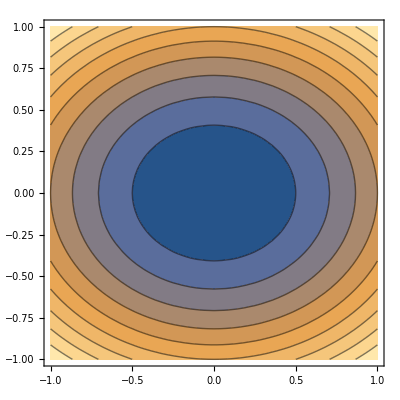

```mathematica
a = 1;
b= 2/3;
x = ContourPlot[x^2 / a  + y^2 / b , {x, -1, 1}, {y, -1, 1}]
```

An ellipses will contain the general equation x^2/a+ y^2/b = c, where a and b are real numbers and c is a constant. The graph was calculated mostly through guess and and check by messing around with the  variable to get circles with contours that are mostly evenly spaced. One data point that I used to check with the original graph is the edges of the ellipses at x = 0.5, when drawing a vertical line, barely intersects the first circle. The lines are mostly evenly spaced throughout the whole graph and level of elevation is at the lowest in the center and gets higher as the graph spans out, much like the original graph.

### Exercise 6:

```mathematica
ContourPlot3D[4(z-2)^2== (x-1)^2+ (y -1)^2   ,{x,-4,6},{y,-4,6},{z,-5,5},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

We are subtracting the values 1,1 and 2 from (x,y,z) respectively in order to translate the double cone graph in the positive direction of x 1 unit, in the positive direction of y 1 unit, and the positive direction of z 1 unit. The equation of a double cone graph is z^2 = A * x^2 + B * y^2 ; in order to get a radius of the cone that intersects the x y plane at zero we multiplied the x and y quantities by 2, so when z=0 and x=1 and y=1, the x and y quantities evaluate to 0, but the z quantity is evaluated to: 4 (-2)^2 which simplifies to 16. And since the radius of the cone is R^2, we can take the square root of 16 and thus we get R = 4.